```mathematica
(* L_v integral for v=1, k^2 < 1 *)
```

```mathematica
Integrate[k2*Sqrt[1-k2*w]/Sqrt[k2*w]*(1-w)^(3/2),{w,0,1}]
```

ConditionalExpression[(2 (-2+k2 (7+3 k2)) EllipticE[k2]+4 (-1+k2) (-1+3 k2) EllipticK[k2])/(15 k2^(3/2)),Im[k2]≠0||Re[k2]≤1]

```mathematica
(* L_v integral for v=0, k^2 < 1 *)
```

```mathematica
Integrate[k2/Sqrt[1-k2*w]/Sqrt[k2*w]*(1-w)^(3/2),{w,0,1}]
```

ConditionalExpression[(2 ((-2+4 k2) EllipticE[k2]+(-1+k2) (-2+3 k2) EllipticK[k2]))/(3 k2^(3/2)),Im[k2]≠0||Re[k2]≤1]

```mathematica
D[Cos[phi]^(2*v-3)*Sin[phi],phi]
```

Cos[phi]^(-2+2 v)-(-3+2 v) Cos[phi]^(-4+2 v) Sin[phi]^2

```mathematica
1-2/10*((2*v-2)*(k2-1)-(2*v-3))
```

1+1/5 (-3+2 v-(-1+k2) (-2+2 v))

```mathematica
FullSimplify[%]
```

-2/5 (k2 (-1+v)-2 v)

```mathematica
(* L_v integral for v=0, k^2 > 1 *)
```

```mathematica
Integrate[1/Sqrt[w]/Sqrt[1-w]*(1-w/k2)^(3/2),{w,0,1}]
```

ConditionalExpression[((-4+8 k2) EllipticE[1/k2]-2 (-1+k2) EllipticK[1/k2])/(3 k2),Im[k2]≠0||Re[k2]≥1||Re[k2]≤0]

```mathematica
(* L_v integral for v=1, k^2 > 1 *)
```

```mathematica
Integrate[1/Sqrt[w]*Sqrt[1-w]*(1-w/k2)^(3/2),{w,0,1}]
```

ConditionalExpression[(2 ((-2+k2 (7+3 k2)) EllipticE[1/k2]+(1+(2-3 k2) k2) EllipticK[1/k2]))/(15 k2),Im[k2]≠0||Re[k2]≥1||Re[k2]≤0]

```mathematica
(* L_v integral for v=2, k^2 > 1 *)
```

```mathematica
Integrate[Sqrt[1-w]/Sqrt[w]*(1-w/k2)^(3/2),{w,0,1}]-Integrate[Sqrt[1-w]*Sqrt[w]*(1-w/k2)^(3/2),{w,0,1}]
```

ConditionalExpression[(2 ((-2+k2 (7+3 k2)) EllipticE[1/k2]+(1+(2-3 k2) k2) EllipticK[1/k2]))/(15 k2)-(2 (-1+2 k2) (8+3 (-1+k2) k2) EllipticE[1/k2]-4 (-1+k2) (2+3 (-1+k2) k2) EllipticK[1/k2])/(105 k2),Im[k2]≠0||Re[k2]≥1||Re[k2]≤0]

```mathematica
FullSimplify[%]
```

ConditionalExpression[(-4 (1+k2) (1+(-6+k2) k2) EllipticE[1/k2]+2 (-1+k2) (-1+k2 (-9+2 k2)) EllipticK[1/k2])/(35 k2),k2≠Re[k2]||Re[k2]≥1||Re[k2]≤0]

```mathematica
L2 = (-4 (1+k2) (1+(-6+k2) k2) EllipticE[1/k2]+2 (-1+k2) (-1+k2 (-9+2 k2)) EllipticK[1/k2])/(35 k2)
```

(-4 (1+k2) (1+(-6+k2) k2) EllipticE[1/k2]+2 (-1+k2) (-1+k2 (-9+2 k2)) EllipticK[1/k2])/(35 k2)

```mathematica
L1 = (2 ((-2+k2 (7+3 k2)) EllipticE[1/k2]+(1+(2-3 k2) k2) EllipticK[1/k2]))/(15 k2)
```

(2 ((-2+k2 (7+3 k2)) EllipticE[1/k2]+(1+(2-3 k2) k2) EllipticK[1/k2]))/(15 k2)

```mathematica
L0 = ((-4+8 k2) EllipticE[1/k2]-2 (-1+k2) EllipticK[1/k2])/(3 k2)
```

((-4+8 k2) EllipticE[1/k2]-2 (-1+k2) EllipticK[1/k2])/(3 k2)

```mathematica
L2 - 1/7*(-(2*k2-8)*L1+(k2-1)*L0)
```

(-4 (1+k2) (1+(-6+k2) k2) EllipticE[1/k2]+2 (-1+k2) (-1+k2 (-9+2 k2)) EllipticK[1/k2])/(35 k2)+1/7 (-((-1+k2) ((-4+8 k2) EllipticE[1/k2]-2 (-1+k2) EllipticK[1/k2]))/(3 k2)-(2 (8-2 k2) ((-2+k2 (7+3 k2)) EllipticE[1/k2]+(1+(2-3 k2) k2) EllipticK[1/k2]))/(15 k2))

```mathematica
FullSimplify[%]
```

0

```mathematica
aqa
```

```mathematica
D[-2/10*Sqrt[k2-1+Cos[phi]^2]^5,phi]
```

Cos[phi] (-1+k2+Cos[phi]^2)^(3/2) Sin[phi]

```mathematica
1+2/10*(2*v-2)
```

1+1/5 (-2+2 v)

```mathematica
FullSimplify[%]
```

1/5 (3+2 v)

```mathematica
Integrate[Cos[phi]^(2v),{phi,-Pi/2,Pi/2}]
```

ConditionalExpression[(√π Gamma[1/2+v])/Gamma[1+v],Re[v]>-1/2]

```mathematica
Integrate[Sin[phi]^(2v),{phi,-Pi/2,Pi/2}]
```

((1+(-1)^(2 v)) √π Gamma[1/2+v])/(2 Gamma[1+v])

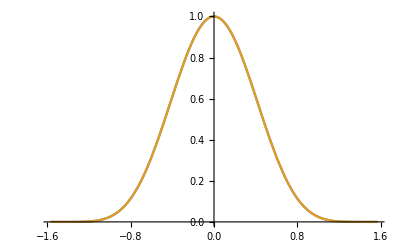

```mathematica
Plot[{Cos[phi]^6,Sin[phi-Pi/2]^6},{phi,-Pi/2,Pi/2}]
```